```mathematica
ρL=1.0; pL=1.0; UL=0.0;
ρR=0.125; pR=0.1; UR=0.0;
```

```mathematica
γ=1.4;
```

```mathematica
aL=√(γ pL/ρL);aR=√(γ pR/ρR);
```

```mathematica
(*-------------------------------*)
α=(γ+1)/(γ-1);
jmp=NSolve[pJump==pL/pR(1-((γ-1)(aR/aL)(pJump-1))/(√(2γ(2γ+(γ+1)(pJump-1)))))^((2γ)/(γ-1)),pJump,Reals][[1]]
```

{pJump→3.0313}

```mathematica
UShock=UR+aR((γ-1+(γ+1)(pJump/.jmp))/(2γ))^(1/2)
```

1.75216

```mathematica
xShock[t_]:=UShock t+0.5
```

```mathematica
UContact=UL+(2 aL)/(γ-1)(1-((pJump/.jmp)pR/pL)^((γ-1)/(2γ)))
```

0.927453

```mathematica
xContact[t_]:=UContact t+0.5
```

```mathematica
xContact[0.2]
```

0.685491

```mathematica
(*-----------------------------------------*)
```

```mathematica
ρ2=((1+α (pJump/.jmp))/(α +(pJump/.jmp)))ρR
```

0.265574

```mathematica
p2=(pJump/.jmp)pR
```

0.30313

```mathematica
U2=UContact
```

0.927453

```mathematica
ρ2 U2
```

0.246307

```mathematica
a2=√(γ p2/ρ2)
```

1.26411

```mathematica
(*-----------------------------------------*)
```

```mathematica
ρ3=((pJump/.jmp)pR/pL)^(1/γ)ρL
```

0.426319

```mathematica
p3=p2
```

0.30313

```mathematica
U3=U2
```

0.927453

```mathematica
ρ3 U3
```

0.395391

```mathematica
a3=√(γ p3/ρ3)
```

0.997725

```mathematica
(*-----------------------------------------*)
```

```mathematica
URareRight=UContact-a3
URareLeft=UL-aL
```

-0.0702728

-1.18322

```mathematica
xRareRight[t_]:=URareRight t +0.5
xRareLeft[t_]:=URareLeft t +0.5
```

```mathematica
xRareRight[0.2]
```

0.485945

```mathematica
xRareLeft[0.2]
```

0.263357

```mathematica
(*-----------------------------------------*)
```

```mathematica
ρ4[x_,t_]:=ρL(2/(γ+1)+(γ-1)/((γ+1)aL)(UL-(x-0.5)/t))^(2/(γ-1))
p4[x_,t_]:=pL(2/(γ+1)+(γ-1)/((γ+1)aL)(UL-(x-0.5)/t))^((2γ)/(γ-1))
U4[x_,t_]:=2/(γ+1)(aL+(γ-1)/2 UL+(x-0.5)/t)
```

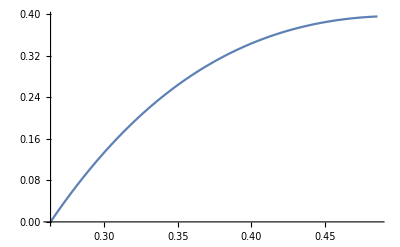

```mathematica
Plot[ρ4[x,0.2]U4[x,0.2],{x,xRareLeft[0.2],xRareRight[0.2]}]
```

```mathematica
ρ4[xRareLeft[0.2],0.2]U4[xRareLeft[0.2],0.2]
```

0.

```mathematica
ρ4[xRareRight[0.2],0.2]U4[xRareRight[0.2],0.2]
```

0.395391

```mathematica
(*--------------------------------------------*)
```

```mathematica
ρ[x_,t_]:=Piecewise[{{ρL,x≤xRareLeft[t]},{ρ4[x,t],xRareLeft[t]<x<xRareRight[t]},{ρ3,xRareRight[t]≤x≤xContact[t]},{ρ2,xContact[t]<x<xShock[t]},{ρR,x≥xShock[t]}}]
```

```mathematica
U[x_,t_]:=Piecewise[{{UL,x≤xRareLeft[t]},{U4[x,t],xRareLeft[t]<x<xRareRight[t]},{U3,xRareRight[t]≤x≤xContact[t]},{U2,xContact[t]<x<xShock[t]},{UR,x≥xShock[t]}}]
```

```mathematica
p[x_,t_]:=Piecewise[{{pL,x≤xRareLeft[t]},{p4[x,t],xRareLeft[t]<x<xRareRight[t]},{p3,xRareRight[t]≤x≤xContact[t]},{p2,xContact[t]<x<xShock[t]},{pR,x≥xShock[t]}}]
```

```mathematica
ρU[x_,t_]=ρ[x,t]U[x,t];
```

```mathematica
e[x_,t_]=p[x,t]/(γ-1)+(ρ[x,t] U[x,t]^2)/2;
```

```mathematica
eint[x_,t_]=p[x,t]/(γ-1);
```

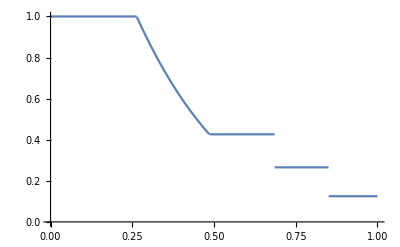

```mathematica
Plot[ρ[x,0.2],{x,0,1}]
```

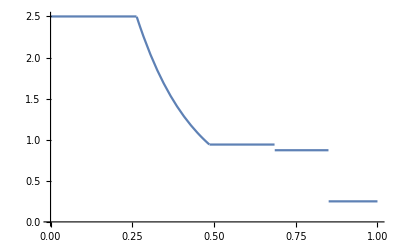

```mathematica
Plot[e[x,0.2],{x,0,1}]
```